## Package import and definitions

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jadeleon/Documents/quantum_chaotic_channels/ja_files

```mathematica
Get["../Mathematica_packages/QMB.wl"]
```

```mathematica
Get["../Mathematica_packages/Chaometer.wl"]
```

## Calculation of superoperators

### Parameters setup

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,2.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,2.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Three initial random states of the environment Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3];
```

### Calculation

```mathematica
superoperators={};
```

```mathematica
AbsoluteTiming[
Do[
AppendTo[superoperators,Superoperator[t,ψ0E[[1]],eigenvalsH,eigenvecsH,L]],
{t,0,50,0.1}]
]
```

{2503.38,Null}

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/regular/superoperators_2.csv",Prepend[superoperators,"L=11;{hx,hz,J}={1.,2.5,ConstantArray[1.,L-1]};SeedRandom[32371];ψ0E=Table[RandomChainProductState[L-1],3];Superoperator[t,ψ0E[[2]],eigenvalsH,eigenvecsH,L];"],"CSV"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/regular/superoperators_2.csv

## Averaged purity and single realizations of dynamics of purity

```mathematica
superoperatorsChaotic=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_2.csv"][[2;;]](*en la posición uno está guardada la información*)];
superoperatorsRegular=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/regular/superoperators_2.csv"][[2;;]](*en la posición uno está guardada la información*)];
```

```mathematica
(*Generate 50 random initial state of the chaometer*)
SeedRandom[94672];
ψ0S=Table[RandomQubitState[],50];
```

```mathematica
(*For each chaometer's random initial state, evolve it with the superoperator and compute its purity*)
purityChaotic=
Table[Chop[
Purity[
ArrayReshape[
#.Flatten[Dyad[ψ0S[[i]]]](* ℰ̂(t).ρ⟩ *),
{2,2}](* ρ⟩ ↦ ρ *)
]&/@superoperatorsChaotic
]
,{i,50}];
```

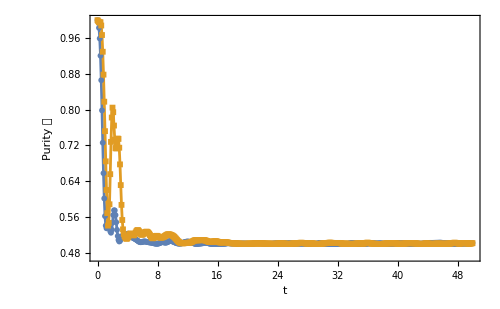

```mathematica
ListPlot[Transpose[{Range[0,50,0.1],#}]&/@purityChaotic[[;;2]],
PlotRange->All,
Joined->True,PlotMarkers->{Automatic, 6},
Frame->True,
FrameLabel->{"t","Purity 𝒫"},
FrameStyle->Directive[Black,FontSize->30,FontFamily->"Arial"],
PlotLegends->Placed[LineLegend[{},LabelStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{Right,Top}],
ImageSize->500]
```

```mathematica
(*For each chaometer's random initial state, evolve it with the superoperator and compute its purity*)
purityRegular=
Table[Chop[
Purity[
ArrayReshape[
#.Flatten[Dyad[ψ0S[[i]]]](* ℰ̂(t).ρ⟩ *),
{2,2}](* ρ⟩ ↦ ρ *)
]&/@superoperatorsRegular
]
,{i,50}];
```

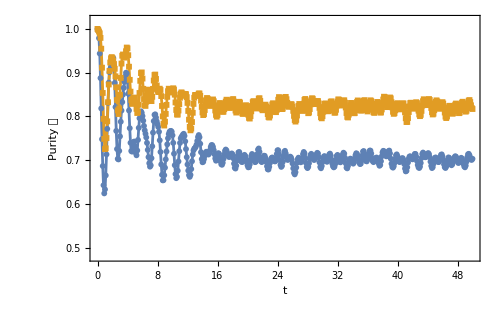

```mathematica
ListPlot[Transpose[{Range[0,50,0.1],#}]&/@purityRegular[[;;2]],
PlotRange->{All,{0.48,1.02}},
Joined->True,PlotMarkers->{Automatic, 6},
Frame->True,
FrameLabel->{"t","Purity 𝒫"},
FrameStyle->Directive[Black,FontSize->30,FontFamily->"Arial"],
PlotLegends->Placed[LineLegend[{},LabelStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{Right,Top}],
ImageSize->500]
```

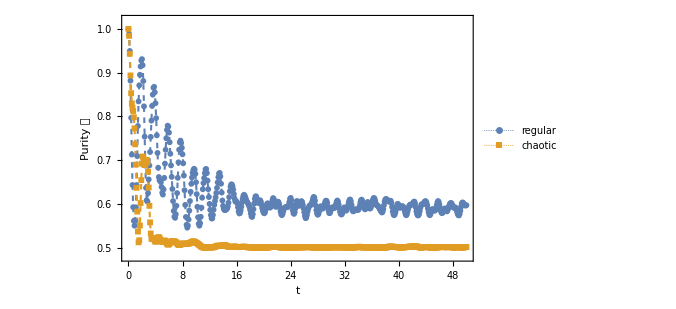

```mathematica
(*Comparison between one chaotic and one regular*)SeedRandom[41];
ListPlot[Transpose[{Range[0,50,0.1],#}]&/@{purityRegular[[RandomInteger[{1,50}]]],purityChaotic[[RandomInteger[{1,50}]]]},
PlotRange->{All,{0.48,1.02}},
Joined->True,
PlotStyle->Directive[Dashing[0.008],Thickness[0.003]],
PlotMarkers->{Automatic,6},
Frame->True,
FrameLabel->{"t","Purity 𝒫"},
FrameStyle->Directive[Black,FontSize->30,FontFamily->"Arial"],
PlotLegends->Placed[LineLegend[{"regular","chaotic"},LabelStyle->{Black,FontFamily->"Arial",FontSize->24},LegendMarkerSize->{40,15}],{Right,Top}],
ImageSize->500]
```

```mathematica
(* Averaged purity for chaotic *)
Total[Total[#*0.1]/50&/@purityChaotic]/50
```

0.515778

```mathematica
(* Averaged purities for chaotic *)
avgPurityChaotic={0.513,0.5168,0.5158}
```

{0.513,0.5168,0.5158}

```mathematica
{Mean[avgPurityChaotic],StandardDeviation[avgPurityChaotic]}
```

{0.5152,0.00196977}

```mathematica
(* Averaged purity for regular *)
Total[Total[#*0.1]/50&/@purityRegular]/50
```

0.6848

```mathematica
(* Averaged purities for regular. Missing second random state *)
avgPurityRegular={0.6748,0.6848,0.6679}
```

{0.6748,0.6848,0.6679}

```mathematica
{Mean[avgPurityRegular],StandardDeviation[avgPurityRegular]}
```

{0.675833,0.00849725}

## Choi matrix’s purity

```mathematica
superoperatorsChaotic=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_"<>ToString[#]<>".csv"][[2;;]](*en la posición uno está guardada la información*)]&/@{1,2,3};
superoperatorsRegular=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/regular/superoperators_"<>ToString[#]<>".csv"][[2;;]](*en la posición uno está guardada la información*)]&/@{1,2,3};
```

```mathematica
AbsoluteTiming[
choiChaoticPurity=Map[Purity[1/2.Reshuffle[#]]&,superoperatorsChaotic,{2}];
]
```

{0.044876,Null}

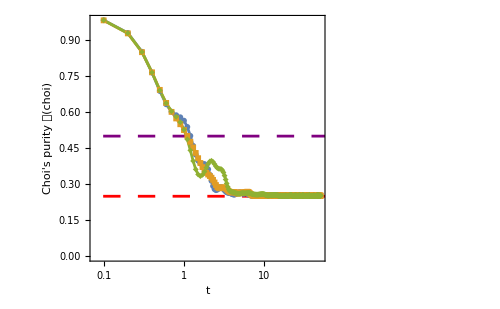

```mathematica
ListLogLinearPlot[Transpose[{Range[0,50,0.1],#}]&/@choiChaoticPurity,
PlotRange->All,
Joined->True,PlotMarkers->{Automatic, 6},
Frame->True,
FrameLabel->{"t","Choi's purity 𝒫(choi)"},
FrameStyle->Directive[Black,FontSize->26,FontFamily->"Arial"],
PlotLegends->Placed[LineLegend[{},LabelStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{Right,Top}],
Epilog->{{Red,Thickness[0.004],Dashing[0.025],InfiniteLine[{{0,0.25},{50,0.25}}]},{Purple,Thickness[0.004],Dashing[0.025],InfiniteLine[{{0,0.5},{50,0.5}}]},Text[Style["chaotic",FontSize->26],{43,0.9}]},
ImageSize->500]
```

```mathematica
AbsoluteTiming[
choiRegularPurity=Map[Purity[1/2.Reshuffle[#]]&,superoperatorsRegular,{2}];
]
```

{0.042777,Null}

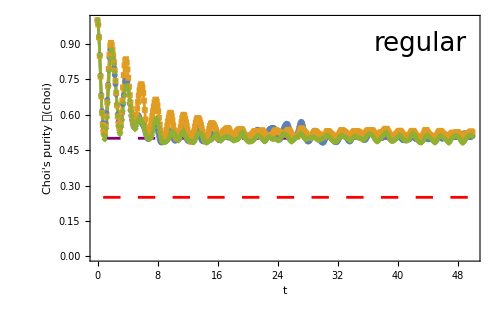

```mathematica
ListPlot[Transpose[{Range[0,50,0.1],#}]&/@choiRegularPurity,
PlotRange->All,
Joined->True,PlotMarkers->{Automatic, 6},
Frame->True,
FrameLabel->{"t","Choi's purity 𝒫(choi)"},
FrameStyle->Directive[Black,FontSize->26,FontFamily->"Arial"],
PlotLegends->Placed[LineLegend[{},LabelStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{Right,Top}],
Epilog->{{Red,Thickness[0.004],Dashing[0.025],InfiniteLine[{{0,0.25},{50,0.25}}]},{Purple,Thickness[0.004],Dashing[0.025],InfiniteLine[{{0,0.5},{50,0.5}}]},Text[Style["regular",FontSize->26],{43,0.9}]},
ImageSize->500]
```

## Comparison, varying number of random states N

```mathematica
superoperatorsChaotic=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_1.csv"][[2;;]](*en la posición uno está guardada la información*)];
superoperatorsRegular=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/regular/superoperators_1.csv"][[2;;]](*en la posición uno está guardada la información*)];
```

```mathematica
(*Generate 50 random initial state of the chaometer*)
SeedRandom[94672];n=5000;
ψ0S=Table[RandomQubitState[],n];
```

```mathematica
(*For each chaometer's random initial state, evolve it with the superoperator and compute its purity*)
purityChaotic=
Table[Chop[
Purity[
ArrayReshape[
#.Flatten[Dyad[ψ0S[[i]]]](* ℰ̂(t).ρ⟩ *),
{2,2}](* ρ⟩ ↦ ρ *)
]&/@superoperatorsChaotic
]
,{i,n}];
```

```mathematica
purityRegular=
Table[Chop[
Purity[
ArrayReshape[
#.Flatten[Dyad[ψ0S[[i]]]](* ℰ̂(t).ρ⟩ *),
{2,2}](* ρ⟩ ↦ ρ *)
]&/@superoperatorsRegular
]
,{i,n}];
```

```mathematica
(*Varying the number of random states: for each chaometer's random initial state, evolve it with the superoperator and compute its purity*)
AbsoluteTiming[purityRegular=
Table[
SeedRandom[94672];
ψ0S=Table[RandomQubitState[],n];
Table[
Chop[
Purity[
ArrayReshape[
#.Flatten[Dyad[ψ0S[[i]]]](* ℰ̂(t).ρ⟩ *),
{2,2}](* ρ⟩ ↦ ρ *)
]&/@superoperatorsRegular
]
,{i,n}]
,{n,50,1000,50}];
]
```

{29.6119,Null}

```mathematica
nn=Range[50,1000,50]
```

{50,100,150,200,250,300,350,400,450,500,550,600,650,700,750,800,850,900,950,1000}

```mathematica
(* Averaged purity for chaotic *)
avgPurity=Table[Total[Total[#*0.1]/50&/@purityRegular[[i]]]/nn[[i]],{i,Length[nn]}]
```

{0.674807,0.695697,0.691299,0.686209,0.681798,0.681549,0.680778,0.681236,0.682791,0.682349,0.684058,0.684283,0.685502,0.684285,0.684221,0.684032,0.683683,0.68162,0.682231,0.68362}

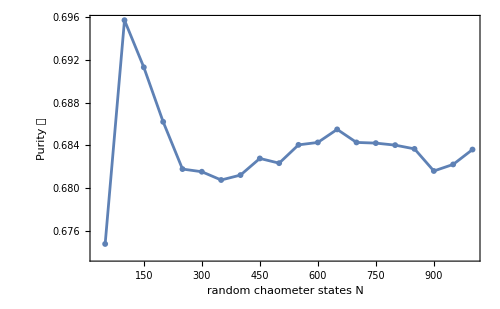

```mathematica
ListPlot[Transpose[{nn,avgPurity}],
PlotRange->All,
Joined->True,PlotMarkers->{Automatic, 6},
Frame->True,
FrameLabel->{"random chaometer states N","Purity 𝒫"},
FrameStyle->Directive[Black,FontSize->25,FontFamily->"Arial"],
PlotLegends->Placed[LineLegend[{},LabelStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{Right,Top}],
ImageSize->500]
```

```mathematica
(* Averaged purity for regular *)
Total[Total[#*0.1]/50&/@purityRegular]/n
```

0.687253